# Optimizing the Time and Place to View Halley’s Comet

## Introduction

Halley’s Comet, designated 1P/Halley, is one of the most famous comets periodically visible to the naked eye on Earth. Halley’s Comet is a short-period comet having an average period of 76 Earth years, and thus it is desired to predict its path and get the best viewing position during its periodic passes near Earth. This essay will explore the prediction of the time where Halley’s Comet is closest to Earth within one period, and approximate where on Earth will be optimal to view the comet.

We can verify that the orbits of Earth and Halley’s Comet are both indeed elliptic by examining each’s orbital eccentricity, which is in the range  for elliptic (and circular) orbits.

Get the entities for Earth and Halley’s Comet:

```mathematica
earth=Entity["Planet","Earth"];
halley=Entity["Comet","Comet1PHalley"];
```

Extract eccentricities:

```mathematica
earth["Eccentricity"]
halley["Eccentricity"]
```

0.01671022

0.96792212

## Extract Orbital Parameters

Since Earth and  Halley’s Comet both orbit the Sun, we will set the Sun as the origin (heliocentric coordinates) and parametrize each orbit with respect to it. We will use the xy-plane as the plane of reference and first parametrize the ellipse on it.
Reconstruction of the shape each object’s orbit requires the location of the foci, or equivalently the center of the ellipse and the vectors representing the semi-major and semi-minor axes. Kepler’s First Law states that for an elliptical orbit around the Sun, the Sun’s center will be at one of the foci of the ellipse. Thus, we can find the center by setting one focus of each orbit as the origin (Sun) and construct the other using the periapsis, which is the closest distance of a satellite to its orbit center during its orbit. Mathematically, it can be shown that this distance is equivalent to the distance from the focus  to the closer vertex  (see figure below). Additionally, the distance between center  and  is thus the length of the semi-major axis, which is a property of a Planet□ and Comet entity.

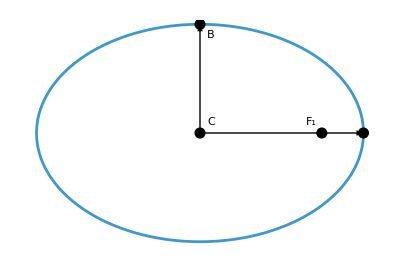

```mathematica
Block[{a=3,b=2,c=Sqrt[a^2-b^2]},
Show[
ParametricPlot[
{a*Cos[t],b*Sin[t]},{t,0,2*Pi},
Axes->False
],
Graphics[{
PointSize[0.02],
Point[{0,0}],Point[{a,0}],Point[{c,0}],Point[{0,b}],
Arrow[{{0,0},{a,0}}],Arrow[{{0,0},{0,b}}]
}],
Epilog->{
Text["C",{0.2,0.2}],
Text["P",{a,0}+{0.2,0.2}],
Text["F_1",{c,0}+{-0.2,0.2}],
Text["B",{0,b}+{0.2,-0.2}]
}
]
]
```

Therefore, we can shift the center to the right by , which is aE-rpE below.

In the cells below, Earth parameters are suffixed with E and Halley’s Comet parameters are suffixed with H.

rpE: Periapsis (AU)

aE: Semi-major axis (AU)

bE: Semi-minor axis (AU)

Get the orbital parameters of Earth describing shape:

```mathematica
rpE=UnitConvert[earth["Periapsis"],"AstronomicalUnit"];
aE=earth["MajorAxis"]/2;
bE=earth["MinorAxis"]/2;
```

The following three parameters are used to uniquely determine the orientation of each orbit, which are analogous to Euler angles and relative to the plane of reference, which we defined as the xy-plane.

iE: Inclination (°)

longAscNE: Longitude of Ascending Node (°)

argPerE: Argument of Periapsis (°)

Get the orbital parameters of Earth describing rotational orientation:

```mathematica
iE=earth["Inclination"];
longAscNE=earth["AscendingNodeLongitude"];
argPerE=earth["PeriapsisArgument"];
```

The next two parameters are used to describe the motion of the object in its parametrized orbit. The last apoapsis time relative to Halley’s Comet’s last apoapsis time is used as the starting point  in the parametric.

nE: Mean motion (rad/a_j)

periodE: Period of the orbit (a_j)

lastApoapsisE: Date of last apoapsis

axialTiltE: Axial tilt of the Earth (°)

Get the orbital parameters of Earth describing motion:

```mathematica
nE=UnitConvert[earth["MeanMotion"],"Radians"/"JulianYears"];
periodE=UnitConvert[earth["OrbitPeriod"],"JulianYears"];
lastApoapsisE=earth["ApoapsisTimeLast"];

axialtiltE=Quantity[23.44,"Degrees"];
```

Get the same parameters from Halley’s Comet:

```mathematica
(* https://en.wikipedia.org/wiki/Orbital_elements *)
rpH=UnitConvert[halley["Periapsis"],"AstronomicalUnit"];
aH=halley["MajorAxis"]/2;
bH=halley["MinorAxis"]/2;

iH=halley["Inclination"];
longAscNH=halley["AscendingNodeLongitude"];
argPerH=halley["PeriapsisArgument"];

nH=UnitConvert[halley["MeanMotion"],"Radians"/"JulianYears"];
periodH=halley["OrbitPeriod"];

lastApoapsisH=halley["ApoapsisTimeLast"];
```

## Solution 1 (Mathematical & Visual Approach): Uniform Parametrization of Orbits

We will carry out the idea described in the previous section. As stated, we will set the points for  as the last time Halley’s Comet was at its apoapsis.

### For Earth

Since Earth’s and Halley’s Comet’s apoapsis clearly does not happen on the same day, we can offset the Earth’s apoapsis by their difference, and convert it to radians. The equation is

```mathematica
apoapsisOffs=2*Pi*QuantityMagnitude[lastApoapsisH-lastApoapsisE,"JulianYears"]/QuantityMagnitude[periodE]
```

-2.7867442

The parametric equation for an ellipse with axes parallel to the xy-axes is given by (

0) from the general equation , which is posE[t_].

Compute the pre-rotated parametric:

```mathematica
centerE={QuantityMagnitude[aE-rpE],0,0};
posE[t_]=centerE+{
QuantityMagnitude[aE]*Cos[t+apoapsisOffs],
QuantityMagnitude[bE]*Sin[t+apoapsisOffs],
0
};
%//MatrixForm
```

(0.0167102+1.0000001 Cos[2.7867442-t]
-0.99986048 Sin[2.7867442-t]
0)

```mathematica
Show[
ParametricPlot3D[posE[t],{t,0,2*Pi}],
Graphics3D[{
Yellow,Ball[{0,0,0},0.2],
Red,Ball[posE[0],0.05]
}]
]
```

-Graphics3D-

```mathematica
emE=EulerMatrix[
{
QuantityMagnitude[UnitConvert[iE,"Radians"]],
QuantityMagnitude[UnitConvert[longAscNE,"Radians"]],
QuantityMagnitude[UnitConvert[argPerE,"Radians"]]
},
{3,1,3}
];
%//MatrixForm
```

(-0.410048 | -0.9120637 | -2.×10^-7
0.8945056 | -0.402155 | 0.1952725
-0.178101 | 0.080071 | 0.98074903)

```mathematica
earthOrbit[t_]= emE.posE[QuantityMagnitude[nE]*t];
earthOrbit[t]//MatrixForm
```

(-0.410048 (0.0167102+1.0000001 Cos[2.7867442-6.283 t])+0.9119365 Sin[2.7867442-6.283 t]
0.8945056 (0.0167102+1.0000001 Cos[2.7867442-6.283 t])+0.402099 Sin[2.7867442-6.283 t]
-0.178101 (0.0167102+1.0000001 Cos[2.7867442-6.283 t])-0.0800598 Sin[2.7867442-6.283 t])

```mathematica
earthPlot=ParametricPlot3D[earthOrbit[t],{t,0,QuantityMagnitude[periodE]}];
Show[
earthPlot,
Graphics3D[{
Yellow,Ball[{0,0,0},0.2],
Red,Ball[earthOrbit[0],0.05]
}]
]
```

-Graphics3D-

### Parametric Orbit for Halley’s Comet

```mathematica
centerH={QuantityMagnitude[aH-rpH],0,0};
posH[t_]={
centerH[[1]]+QuantityMagnitude[aH]*Cos[t],
centerH[[2]]+QuantityMagnitude[bH]*Sin[t],
centerH[[3]]
};
%//MatrixForm
Show[
ParametricPlot3D[posH[t],{t,0,2*Pi}],
Graphics3D[{
Yellow,Ball[{0,0,0},0.4],
Blue,Ball[posH[0],0.3]
}]
]
```

(17.354877+17.9300343 Cos[t]
4.504929 Sin[t]
0)

-Graphics3D-

```mathematica
emH=EulerMatrix[
{
QuantityMagnitude[UnitConvert[iH,"Radians"]],
QuantityMagnitude[UnitConvert[longAscNH,"Radians"]],
QuantityMagnitude[UnitConvert[argPerH,"Radians"]]
},
{3,1,3}
];
%//MatrixForm
```

(0.21445 | 0.940857 | 0.262299
-0.568626 | -0.098088 | 0.816727
0.794152 | -0.324295 | 0.513961)

```mathematica
halleyOrbit[t_]=emH.posH[QuantityMagnitude[nH]*t];
halleyOrbit[t]//MatrixForm
```

(0.21445 (17.354877+17.9300343 Cos[0.0827560942 t])+4.23849 Sin[0.0827560942 t]
-0.568626 (17.354877+17.9300343 Cos[0.0827560942 t])-0.44188 Sin[0.0827560942 t]
0.794152 (17.354877+17.9300343 Cos[0.0827560942 t])-1.46093 Sin[0.0827560942 t])

```mathematica
halleyPlot=ParametricPlot3D[halleyOrbit[t],{t,0,QuantityMagnitude[periodH]}];
Show[
halleyPlot,
Graphics3D[{
Yellow,Ball[{0,0,0},0.4],
Blue,Ball[halleyOrbit[0],0.3]
}],
ViewPoint->{1,2,2}
]
```

-Graphics3D-

### Combined Plots

```mathematica
Show[
halleyPlot,
earthPlot,
Graphics3D[{
Yellow,Ball[{0,0,0},0.4],
Red,Ball[posE[0],0.3],
Blue,Ball[halleyOrbit[0],0.3]
}],
ViewPoint->{-2,4,2}
]
```

-Graphics3D-

### Minimization

```mathematica
d[t_]=EuclideanDistance[earthOrbit[t],halleyOrbit[t]];
```

```mathematica
yearOffset=QuantityMagnitude[DateDifference[lastApoapsisH,Now],"JulianYears"]
itv={0,QuantityMagnitude[periodE*periodH]}+yearOffset;

NMinimize[{d[x],Between[x,itv]},{x}];

dist=Quantity[%[[1]],"AstronomicalUnit"]
time=Quantity[%%[[2,1,2]],"JulianYears"]
```

1.42759

0.23588 au

40.605 a

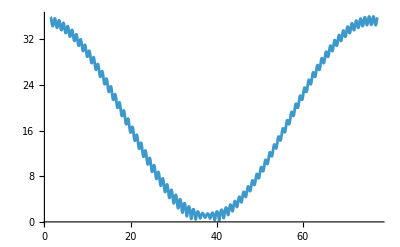

```mathematica
Plot[d[x],Prepend[itv,x]]
```

## Solution 2 (Data Approach): Astronomical Computation Built-ins

Sets the `time` and `dist` variables to the solutions found.

```mathematica
itv={0,QuantityMagnitude[periodE*periodH]}+N[DateValue["Year"]];

newtime=NMinimize[
{
QuantityMagnitude[AstroDistance[halley,Dated[earth,x]]],
Between[x,itv]
},
{x}
];

dist=Quantity[%[[1]],"AstronomicalUnit"]
time=Quantity[%%[[2,1,2]]-DateValue[lastApoapsisE,"Year"],"JulianYears"]
```

AstroDistance::date: Expression Earth cannot be interpreted as a date specification.

General::stop: Further output of AstroDistance::date will be suppressed during this calculation.

0.344372 au

37.8732 a

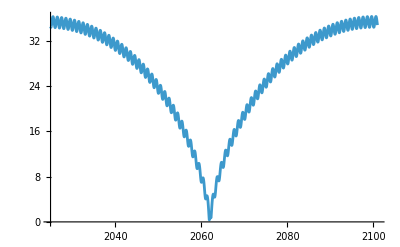

```mathematica
Plot[AstroDistance[halley,Dated[earth,x]],Prepend[itv,x]]
```

## Answer

```mathematica
DatePlus[CurrentDate["Hour"],time-Quantity[yearOffset,"JulianYears"]];
DateString[%]
```

Fri 9 Dec 2061 4 am

```mathematica
time
```

37.8732 a

```mathematica
mtime=QuantityMagnitude[time];(* julian years *)
rotTE=QuantityMagnitude[earth["RotationPeriod"],"Hours"];(* hours *)
rotdxE=QuantityMagnitude[time,"Hours"]/rotTE; (* rots *)
rotdxE=SetPrecision[(rotdxE-Floor[rotdxE])*360,8];
angcoords=ToSphericalCoordinates[halleyOrbit[mtime]-earthOrbit[mtime]][[2;;3]]*180/Pi
```

{117.066,92.6488}

```mathematica
lat=90-angcoords[[1]]+QuantityMagnitude[axialtiltE];
long=Mod[angcoords[[2]]-rotdxE,360];
If[lat>90,Print[long=Mod[long+180,360]];lat-=90];
pos=GeoPosition[{lat,long}]
```

GeoPosition[{-3.62616,70.3241}]

```mathematica
GeoNearest["City",pos];
GeoListPlot[%,GeoLabels->Automatic,GeoRange->"Country"]
Show[
GeoListPlot[%%,GeoLabels->Automatic,GeoRange->"World"],
GeoGraphics[GeoPath[{"Parallel",lat}]]
]
```

GeoGraphics::entgr: Unable to find geo range implied by GeoRange->Country.

-Graphics-

-Graphics-

```mathematica
Show[
halleyPlot,
earthPlot,
Graphics3D[{
Red,Ball[earthOrbit[mtime],0.4],
Blue,Ball[halleyOrbit[mtime],0.1]
}],
PlotRange->{{-1,2},{-2,1},{-1.5,2}},
ViewPoint->{-2, 4, 0}
]
```

-Graphics3D-